```mathematica
ArcCos[0.957]
```

0.294319

```mathematica
N[0.29431870450315556/°]
```

16.8632

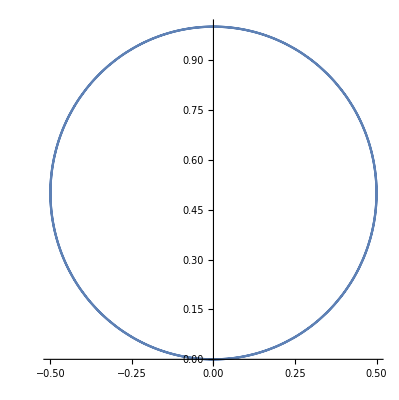

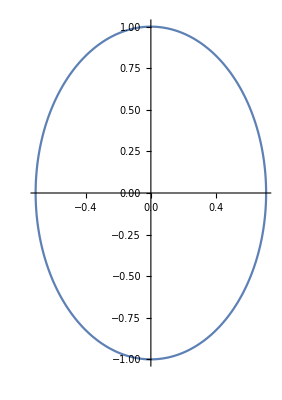

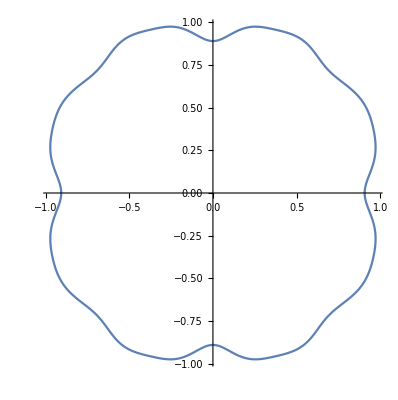

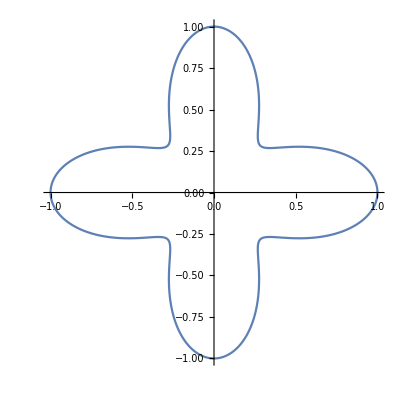

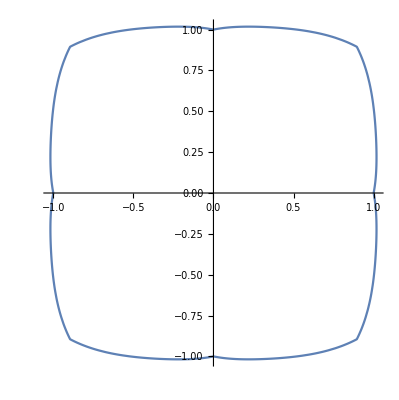

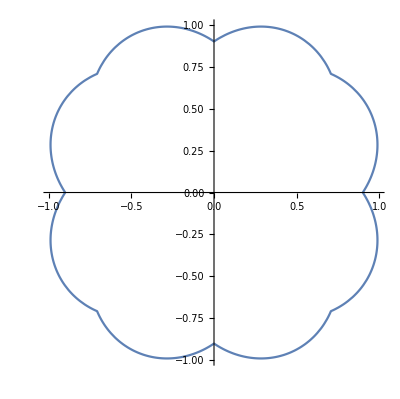

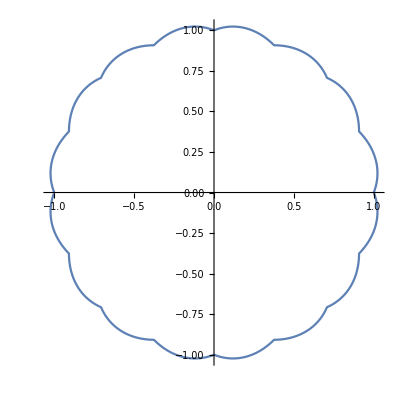

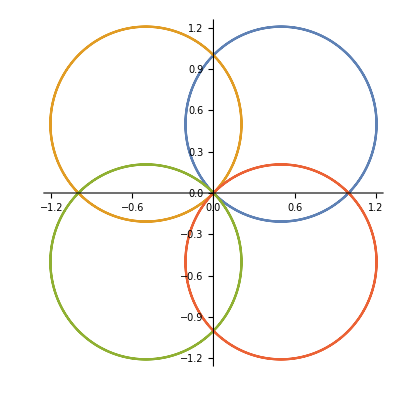

```mathematica
a0 = 1; (* san = (neg x 1) *) 
neg = -1;
b0 =1/(√(1*Cos[θ-Pi/2]^2+2Sin[θ-Pi/2]^2));

b00 =Cos[θ-Pi/2];
(* basis function of zero order - offset *)
(* plot basis functions bij with their corresponding coeff. an/bn *)
b11=Cos[θ] + Sin[θ]; b12 = neg*Cos[θ] + Sin [θ];b13 = neg*Cos[θ] + neg*Sin [θ];b14 = Cos[θ] + neg*Sin [θ];b21=Cos[2θ] + Sin [2θ]; b22 = neg*Cos[2θ] + Sin [2θ];b23 = neg*Cos[2θ] + neg*Sin [2θ];b24 = Cos[2θ] + neg*Sin [2θ];b31=Cos[3θ] + Sin [3θ]; b32 = neg*Cos[3θ] + Sin [3θ];b33 = neg*Cos[3θ] + neg*Sin [3θ];b34 = Cos[3θ] + neg*Sin [3θ];
b4 = 0.3Cos[4θ]+ 0.7;
b5 =0.4(Abs[Sin[θ]]+Abs[Cos[θ]])+0.1Abs[Sin[2θ]]-0.1Abs[Sin[4θ]]+ 0.6;
b6= Abs[0.2 Sin[2 θ]]+0.2 Abs[Cos[2 θ]]+0.1 Abs[Cos[4 θ]]+0.7;
b7= Abs[0.3 Sin[2 θ]]+0.2 Abs[Cos[2 θ]]+0.7;
b8= 1.0 + 0.0015Cos[2θ] -0.043Cos[4θ]+ 0.0013Cos[6θ] -0.042Cos[8θ] + 0.002Cos[10θ] -0.0043Cos[12θ]+ 0.0013Cos[14θ] -0.01Cos[16θ]+ 0.002Cos[18θ] -0.002Cos[20θ];
b9= 1.0 + 0.0018Cos[2θ] -0.0005Cos[4θ]+ 0.0003Cos[6θ] +0.008Cos[8θ] + 0.002Cos[10θ] -0.00042Cos[12θ]+ 0.001Cos[14θ] -0.01Cos[16θ]+ 0.004Cos[18θ] -0.0007Cos[20θ];
b10= 1.5 + 0.256Cos[2θ] -0.16Cos[4θ]+ 0.02Cos[6θ] +0.004Cos[8θ] + 0.009Cos[10θ] -0.01Cos[12θ]+ 0.006Cos[14θ] -0.002Cos[16θ]+ 0.003Cos[18θ] -0.007Cos[20θ]; (* box: Härtetest: fiesestes Profil *)
PolarPlot[{b00},{θ,0,2 Pi}]
PolarPlot[{b0},{θ,0,2 Pi}]
PolarPlot[{b8},{θ,0,2 Pi}]
PolarPlot[{b4},{θ,0,2 Pi}]
PolarPlot[{b5},{θ,0,2 Pi}]
PolarPlot[{b7},{θ,0,2 Pi}]
PolarPlot[{b6},{θ,0,2 Pi}]
PolarPlot[{b11,b12,b13,b14},{θ,0,2Pi}]
PolarPlot[{b21,b22,b23,b24},{θ,0,2 Pi}]
PolarPlot[{b31,b32,b33,b34},{θ,0,2 Pi}]
```

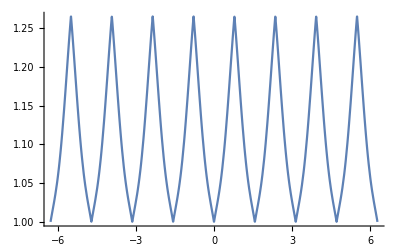

```mathematica
Plot[0.4(Abs[Sin[θ]]+Abs[Cos[θ]])+0.1Abs[Sin[2θ]]-0.1Abs[Sin[4θ]]+ 0.6, {θ, -2Pi, 2Pi}] (* cartesian synonym plot for polar plot on domain of θ*)
```

```mathematica
'
```

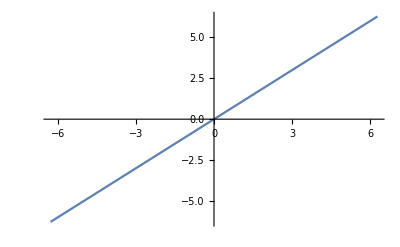

```mathematica
Plot[θ, {θ, -2Pi, 2Pi}]
```

```mathematica
∫_-Pi^Pi Cos[4θ]*(0.7+0.3Cos[4θ])ⅆθ
```

0.942478

```mathematica
%/Pi
```

0.3

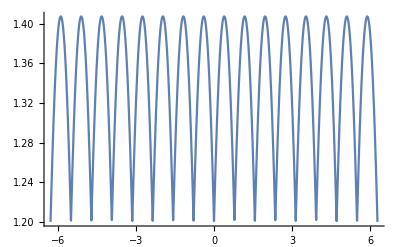

```mathematica
Plot[Abs[0.5 Sin[2 θ]]+0.5 Abs[Cos[2 θ]]+0.7, {θ, -2Pi, 2Pi}]
```

```mathematica
FourierTransform[x^2,x,w]
```

-√(2 π) DiracDelta''[w]

-(Sqrt[2*Pi]*Derivative[2][DiracDelta][w])

WolframAlphaQueryResults